## INTRO

💡 This is a program for χ^2 fitting, using SN1a data.
💡 SN data are taken from http://supernova.lbl.gov/Union/
💡 
💡
💡

## PRE

### Settings

Include the packages needed.

```mathematica
Needs["ErrorBarPlots`"]
<<PhysicalConstants`
```

```mathematica
Needs["PlotLegends`"]
```

Set work directory. Modify it to your own directory before runing this program. DATA folder are placed in this directory. DATA folder should contain the SN data files.

```mathematica
SetDirectory["E:\\Nutshare\\Store\\Projects\\DataFitting"];
```

### Conventions, parameters, etc

Line element: ds^2=-dt^2+a[t]^2(dr^2/(1-k r^2)+r^2(dθ^2+Sin[θ]^2 dϕ^2))

Ωm0: matter fraction
Ωd0: dark energy/cosmological constant fraction
Ωr0: radiation fraction

Ωm0w: matter fraction given by WMAP
Ωd0w: dark energy/cosmological constant fraction given by WMAP
Ωr0w: radiation fraction given WMAP

```mathematica
Ωm0w=0.27;
Ωd0w=0.73;
Ωr0w =8.09*10^-5;
```

### Basic Equations in LCDM

H0: Hubble constant in unit of km/s/Mpc
c: speed of light

```mathematica
H0w=71;
c=SpeedOfLight*Second/(1000Meter)
gra=GravitationalConstant
```

149896229/500

(6.67428×10^-11 Meter^2 Newton)/Kilogram^2

## LCDM Model

### Basic Definations

hubble[Ωm0_,Ωd0_,Ωk0_,z_]: Hubble functions in LCDM.
H[z]: an example of hubble function with given parameters.

```mathematica
hubble[Ωm0_,Ωd0_,Ωk0_,z_]:=H0w √(Ωm0(1+z)^3+Ωd0+Ωk0(1+z)^2);
H[z_]=hubble[Ωm0w,Ωd0w,0,z];
```

q[Ωm0_,Ωd0_,Ωk0_,z_]:Deceleration parameter. DEF: q[Ωm0_,Ωd0_,Ωk0_,z_]=-1/H[z]D[D[a[t],t],t]/D[a[t],t]

```mathematica
q[Ωm0_,Ωd0_,Ωk0_,z_]=-1+(1+z)/hubble[Ωm0,Ωd0,Ωk0,z] D[hubble[Ωm0,Ωd0,Ωk0,z],z];
```

```mathematica
q[Ωm0,Ωd0,Ωk0,0]
```

-1+(2 Ωk0+3 Ωm0)/(2 (Ωd0+Ωk0+Ωm0))

```mathematica
Limit[q[Ωm0,Ωd0,Ωk0,z],z->Infinity]
```

1/2

(General) Friedmann equations are

(3(a[t]'+k))/a[t]^2=8 π G ρ
2(a[t]'')/a[t]+(a[t]'+k)/a[t]^2=-8π G p

Since “zt” will be used as a parameter in most cases, we define “ztr” as a name for transition redshift, “ztrr” for transition redshift with a parameter r.
ztr[Ωm0_,Ωd0_,z_]: Transition redshift in LCDM with Ωk0 not zero with full parameters
ztrr[r_,z_]: with r=Ωm0/Ωd0

```mathematica
ztr[Ωm0_,Ωd0_]=(2 Ωd0/Ωm0)^(1/3)-1;
ztrr[r_]=(2/r)^(1/3)-1;
```

Regard “zt” as a paramter, solve out Ωd0 and Ωk0=1-Ωm0-Ωd0

Ωd0=1/2 Ωm0(1+zt)^3
Ωk0=1-Ωm0-1/2 Ωm0(1+zt)^3

### Transition redshift, deceleration parameter, theoretically.

#### Deceleration parameter

Deceleration parameter can be ploted with respect to redshift z.
Using flat FRW model. That is Ωk0=0.

```mathematica
pldec[Ωm0v_,color_]:=Plot[q[Ωm0v,1-Ωm0v,0,z],{z,-1,10},PlotRange->{{-1.05,10},{-1.05,0.55}},PlotStyle->color,AxesOrigin->{-1,0},AxesLabel->{z,q}]
```

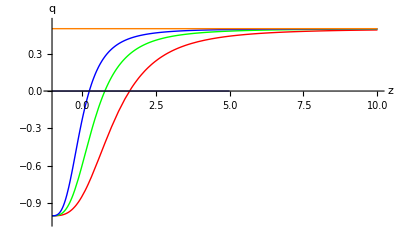

```mathematica
Show[{pldec[0.1,Red],pldec[0.26,Green],pldec[0.5,Blue],pldec[1,Orange],Plot[0,{z,-1,5},PlotStyle->Thick]}]
```

```mathematica
Manipulate[pldec[Ωm0v,{Orange,Thick}],{{Ωm0v,0.26,"Matter Fraction"},0,1,Appearance->"Open"},SaveDefinitions->True]
```

Plot deceleration parameter with respect to r. This is not related to Ωk0, i.e., the curvature of the spacetime won’t affect this result.

```mathematica
plztr[color_]:=Plot[ztr[Ωm0,1-Ωm0],{Ωm0,0,1},PlotRange->{{0,1},{-1,4}},PlotStyle->color,AxesOrigin->{0,-1}]
```

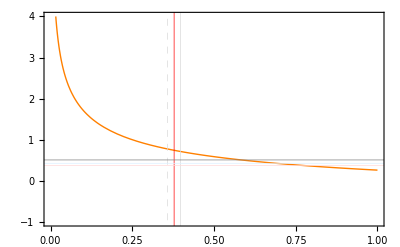

```mathematica
pldecr=Plot[ztrr[r],{r,0,1},PlotRange->{{0,1},{-1,4}},PlotStyle->{Thick,Orange},AxesOrigin->{0,-1},Frame->True,GridLines->{{{0.358,Dashed},{0.378,Directive[Red]},0.398},{{0.376,LightRed},{0.426,LightBlue},{0.508,Gray}}}]
```

In a flat universe, Ωk0=0. Then Ωd0=1-Ωm0.

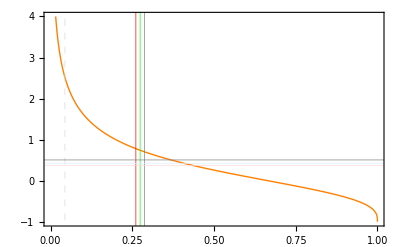

```mathematica
pldecr=Plot[ztr[Ωm0,1-Ωm0],{Ωm0,0,1},PlotRange->{{0,1},{-1,4}},PlotStyle->{Thick,Orange},AxesOrigin->{0,-1},Frame->True,GridLines->{{{0.044,Dashed},{0.261,Red},{0.274,Green},{0.287,Gray}},{{0.376,LightRed},{0.426,LightBlue},{0.508,Gray}}}]
```

## Interacting Models

### Take the form Q_c=ξ H ρ_c.

Hubble function without curvature

```mathematica
hubbleICC[H0_,Ωd0_,Ωm0_,w_,ξ_,z_]:=H0 √(Ωm+Ωd);
```

### δ is constant + EoS w is constant

#### Definations

Fraction energy density

```mathematica
ΩmICC[Ωm0_,ξ_,z_]:=Ωm0 (1+z)^(3-ξ)
```

```mathematica
ΩdICC[Ωm0_,Ωd0_,w_,ξ_,z_]:=Ωd0 (1+z)^(3(1+w))-ξ/(ξ+3w) Ωm0 (1+z)^(3(1+w))((1+z)^(-ξ-3w)-1)
```

Hubble function

```mathematica
hubbleICC[H0ICC_,Ωm0ICC_,Ωd0ICC_,wICC_,ξICC_,z_]=H0ICC √(ΩmICC[Ωm0ICC,ξICC,z]+ΩdICC[Ωm0ICC,Ωd0ICC,wICC,ξICC,z])
```

H0ICC √((1+z)^(3 (1+wICC)) Ωd0ICC+(1+z)^(3-ξICC) Ωm0ICC-((1+z)^(3 (1+wICC)) (-1+(1+z)^(-3 wICC-ξICC)) ξICC Ωm0ICC)/(3 wICC+ξICC))

Deceleration parameter

```mathematica
qICC[H0ICC_,Ωm0ICC_,Ωd0ICC_,wICC_,ξICC_,z_]=-1+(1+z)/hubbleICC[H0ICC,Ωm0ICC,Ωd0ICC,wICC,ξICC,z] D[hubbleICC[H0ICC,Ωm0ICC,Ωd0ICC,wICC,ξICC,z],z];
```

```mathematica
qICC[H0ICC,Ωm0ICC,Ωd0ICC,wICC,ξICC,z]//FullSimplify
```

(-3 wICC (-1+ξICC) Ωm0ICC+(1+3 wICC) (1+z)^(3 wICC+ξICC) (3 wICC Ωd0ICC+ξICC (Ωd0ICC+Ωm0ICC)))/(6 wICC Ωm0ICC+2 (1+z)^(3 wICC+ξICC) (3 wICC Ωd0ICC+ξICC (Ωd0ICC+Ωm0ICC)))

```mathematica
Limit[qICC[H0ICC,Ωm0ICC,Ωd0ICC,wICC,ξICC,z]//FullSimplify,z->Infinity,Assumptions->(3 wICC+ξICC)<0]
```

(1-ξICC)/2

At z-> Infinity limit, qIIC->(1-ξ)/2, with 3 wICC+ξICC<0. This is different from LCDM model.

#### Plots, showcase, manipulate toys

```mathematica
pldecICC[Ωm0ICC_,wICC_,ξICC_,color_]:=Plot[qICC[H0w,Ωm0ICC,1-Ωm0ICC,wICC,ξICC,z],{z,-1,10},PlotRange->{{-1.05,10},{-1.05,1}},PlotStyle->color,AxesOrigin->{-1,0},AxesLabel->{z,q}];
```

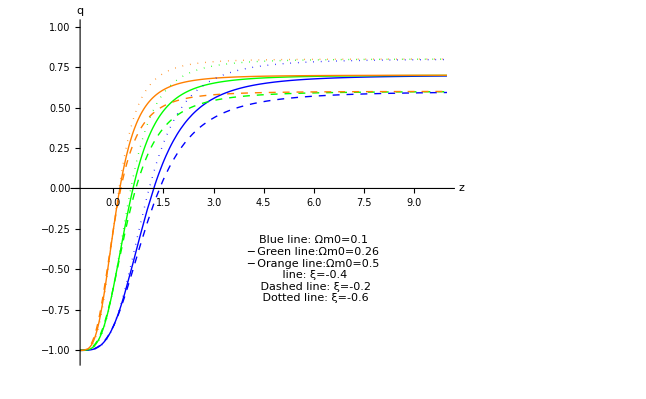

```mathematica
pldecICCShowSum=Show[{pldecICC[0.1,-1,-0.4,Blue],pldecICC[0.26,-1,-0.4,Green],pldecICC[0.5,-1,-0.4,Orange],pldecICC[0.1,-1,-0.2,Directive[Blue,Dashed]],pldecICC[0.26,-1,-0.2,Directive[Green,Dashed]],pldecICC[0.5,-1,-0.2,Directive[Orange,Dashed]],pldecICC[0.1,-1,-0.6,Directive[Blue,Dotted]],pldecICC[0.26,-1,-0.6,Directive[Green,Dotted]],pldecICC[0.5,-1,-0.6,Directive[Orange,Dotted]]},Epilog->Inset[Framed[Style["Blue line: Ωm0=0.1\n─ Green line:Ωm0=0.26\n─ Orange line:Ωm0=0.5\n line: ξ=-0.4\n Dashed line: ξ=-0.2\n Dotted line: ξ=-0.6",10],Background->LightYellow],{6,-0.5}]]
```

z->Infinity is a degenerate limit. For constant ξ and constant w models, this limit is determined by the interaction strength ξ . This might be useful if more complicated models are investigated and no large deviations are shown. [Nota]

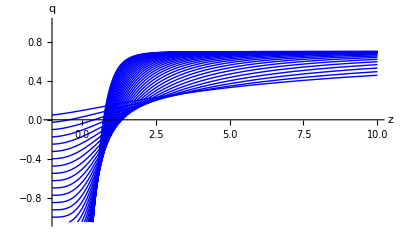
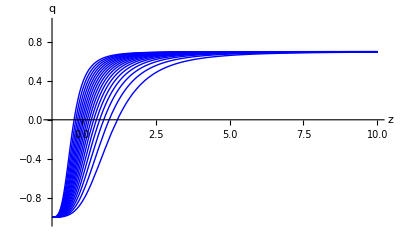
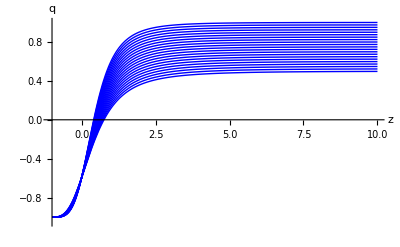
Varying EoS | Varying Ωm0 | Varying ξ
-Graphics- | -Graphics- | -Graphics-

```mathematica
varyingICCShowSum=Grid[{{"Varying EoS","Varying Ωm0","Varying ξ"},Table[{Show[Table[pldecICC[0.1,wICC,-0.4,Blue],{wICC,-2,-0.3,0.05}]],Show[Table[pldecICC[Ωm0ICC,-1,-0.4,Blue],{Ωm0ICC,0.1,0.9,0.05}]],Show[Table[pldecICC[0.27,-1,ξICC,Blue],{ξICC,-1,0,0.05}]]}]},Frame->All]
```

Interaction ξ changes the limit, i.e., what value will it be at z->Infinity. EoS changes the the whole shape. Matter fraction also changes how fast q varies, but just in a small time scale.

Use movable slides to check how do the parameters affect the deceleration parameter. Just a toy.

```mathematica
pldecICCManSum=Manipulate[Show[{pldecICC[Ωm0ICC,wICC,ξICC,Orange],pldec[Ωm0ICC,{Pink,Thick}]}],{{Ωm0ICC,0.26,"Matter Fraction"},0,1,Appearance->"Open"},{{ξICC,-0.4,"Interaction"},-1,0,Appearance->"Open"},{{wICC,-1,"Equation of State"},-1.5,-0.5,Appearance->"Open"},Delimiter,Style["Pink is the deceleration parameter for LCDM.",Medium],Style["Orange is for interacting model with Q=ξ H ρ_m",Medium],ControlPlacement->{Right,Right,Right},SaveDefinitions->True]
```

#### Transition redshift definations and equations.

Find out the expression for transition redshift

```mathematica
(3wICC+1)ΩdICC[Ωm0ICC,Ωd0ICC,wICC,ξICC,z]+ΩmICC[Ωm0ICC,ξICC,z]==0//Simplify
```

(1+z)^(3-ξICC) Ωm0ICC+(1+3 wICC) (1+z)^(3+3 wICC) (Ωd0ICC+((1-(1+z)^(-3 wICC-ξICC)) ξICC Ωm0ICC)/(3 wICC+ξICC))==0

```mathematica
ztrICC[Ωm0ICC_,Ωd0ICC_,wICC_,ξICC_]=-1+((-ξICC/(ξICC+3wICC)(1+3wICC)+1)/((1+3wICC)(-ξICC/(ξICC+3wICC)Ωm0ICC-Ωd0ICC))Ωm0ICC)^(1/(ξICC+3wICC))
```

-1+(((1-((1+3 wICC) ξICC)/(3 wICC+ξICC)) Ωm0ICC)/((1+3 wICC) (-Ωd0ICC-(ξICC Ωm0ICC)/(3 wICC+ξICC))))^(1/(3 wICC+ξICC))

The first solution is trivil. So the second one is taken.

Define rICC=Ωm0ICC/Ωd0ICC

```mathematica
ztrrICC[rICC_,wICC_,ξICC_]=-1+((-ξICC/(ξICC+3wICC)(1+3wICC)+1)/((1+3wICC)(-ξICC/(ξICC+3wICC)rICC-1))rICC)^(1/(3 wICC+ξICC));
```

#### Visualiztion of transition redshift

Check the behavior of this transition redshift.

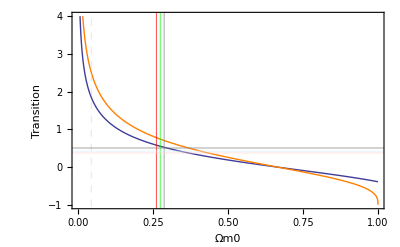

```mathematica
pldecrICC=Plot[{ztrICC[Ωm0ICC,1-Ωm0ICC,-1,-0.4],ztr[Ωm0ICC,1-Ωm0ICC]},{Ωm0ICC,0,1},FrameLabel->{"Ωm0","Transition"},PlotRange->{{0,1},{-1,4}},PlotStyle->{Thick,Orange},AxesOrigin->{0,-1},Frame->True,PlotRangeClipping->False,GridLines->{{{0.044,Dashed},{0.261,Red},{0.274,Green},{0.287,Gray}},{{0.376,LightRed},{0.426,LightBlue},{0.508,Gray}}},PlotLegend->{"Q=-0.4 H ρ_c","LCDM"},LegendPosition->{1.1,-0.4}]
```

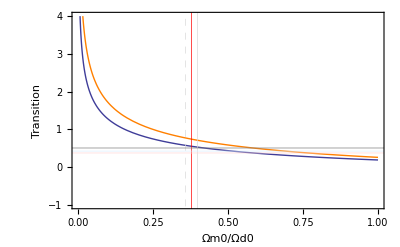

```mathematica
pldecrrICC=Plot[{ztrrICC[rICC,-1,-0.4],ztrr[rICC]},{rICC,0,1},PlotRange->{{0,1},{-1,4}},PlotStyle->{Thick,Orange},AxesOrigin->{0,-1},Frame->True,FrameLabel->{"Ωm0/Ωd0","Transition"},GridLines->{{{0.358,Dashed},{0.378,Directive[Red]},0.398},{{0.376,LightRed},{0.426,LightBlue},{0.508,Gray}}},PlotLegend->{"Q=-0.4 H ρ_c","LCDM"},LegendPosition->{1.1,-0.4}]
```

```mathematica
plztrICC[wICC_,ξICC_,color_]:=Plot[ztrICC[Ωm0ICC,1-Ωm0ICC,wICC,ξICC],{Ωm0ICC,0,1},PlotRange->{{0,1},{-1,4}},PlotStyle->color,AxesOrigin->{0,-1},Frame->True];
```

```mathematica
Show[plztrICC[-1,-0.02,Orange],Graphics[{Gray,Rectangle[Scaled[{0.358,.2752}],Scaled[{0.398,.3016}]]},Frame->True],FrameLabel->{"Ωm0","Transition"}]
```

-Graphics-

```mathematica
plztrICCManSum=Manipulate[Show[{plztrICC[wICC,ξICC,Orange],Plot[ztr[Ωm0ICC,1-Ωm0ICC],{Ωm0ICC,0,1},PlotRange->{{0,1},{-1,4}},PlotStyle->Pink,AxesOrigin->{0,-1}]},Graphics[{Gray,Rectangle[Scaled[{0.358,.2752}],Scaled[{0.398,.3016}]]},Frame->True],FrameLabel->{"Ωm0","Transition"}],{{ξICC,-0.4,"Interaction"},-1,1,Appearance->"Open"},{{wICC,-1.02,"Equation of state"},-2,-0.3,Appearance->"Open"},Delimiter,Style["Pink is the transition redshift vs Ωm0 for LCDM.",Medium],Style["Orange is for interacting model with Q=ξ H ρ_m,",Medium],Style["where ξ is constant and EoS is constant",Medium],ControlPlacement->{Right,Right},SaveDefinitions->True]
```

#### Find out the allowed region of coupling constant.

To find out the region of ξ, set w=-1 and Ωd0=1-Ωm0. Let the ztr-Ωm0 line cross points (0.287,0.508) and (0.261, 0.376).

```mathematica
ztrICC[0.287,1-0.287,-1,ξICC1]==0.508
```

-1+0.1435^(1/(-3+ξICC1)) (-(1+(2 ξICC1)/(-3+ξICC1))/(-0.713-(0.287 ξICC1)/(-3+ξICC1)))^(1/(-3+ξICC1))==0.508

```mathematica
ξICCffunc[Ωm0ICC_,Ωd0ICC_,wICC_,data_]:=ξICC/.FindRoot[ztrICC[Ωm0ICC,Ωd0ICC,wICC,ξICC]==data,{ξICC,-0.6}]
```

```mathematica
ξICCf2[Ωm0ICC_,Ωd0ICC_,wICC_]:=ξICC/.FindRoot[ztrICC[Ωm0ICC,Ωd0ICC,wICC,ξICC]==0.508,{ξICC,-0.6}]
```

```mathematica
ξICCf1[Ωm0ICC_,Ωd0ICC_,wICC_]:=ξICC/.FindRoot[ztrICC[Ωm0ICC,Ωd0ICC,wICC,ξICC]==0.376,{ξICC,-0.6}]
```

Cross the Center of best fit. (0.274,0.426)

```mathematica
ξICCfc[Ωm0ICC_,Ωd0ICC_,wICC_]:=ξICC/.FindRoot[ztrICC[Ωm0ICC,Ωd0ICC,wICC,ξICC]==0.426,{ξICC,-0.6}]
```

According to the data of transition redshift.

```mathematica
ξICCf2[wICC_]:=ξICCffunc[0.287,1-0.287,wICC,0.508]
```

```mathematica
ξICCf1[wICC_]:=ξICCffunc[0.261,1-0.261,wICC,0.376]
```

```mathematica
ξICCfc[wICC_]:=ξICCffunc[0.274,1-0.274,wICC,0.426]
```

```mathematica
numPlot[ss1_,{s_,c_,e_},ee_,{start_,end_}]:=Graphics[{Orange,Thickness[.01],Text[Style[ss1,Large,Orange],{s,0}],Text[Style["|",Large,Orange],{c,0}],Text[Style[ee,Large,Orange],{e,0}],Line[{{s,0},{e,0}}]},Axes->{True,False},AxesStyle->Directive[Thin,Black,12],PlotRange->{{start,end},{0,0}},AspectRatio->0.1]
```

```mathematica
fitξICCManSum=Manipulate[{numPlot["(",{ξICCf1[wICC],ξICCfc[wICC],ξICCf2[wICC]},")",{-1.5,1}],{ξICCf1[wICC],ξICCfc[wICC],ξICCf2[wICC]}},{{wICC,-1,"Equation of State"},-3,-0.47,Appearance->"Open"},Delimiter,Style["This is the fitting result from transition redshift data.",Bold],Delimiter,"The parenthesis shows the upper and lower value \n while the verticle line show the center value.",Style["\n The three numbers are left value, center value, right value respectively."],Delimiter,Delimiter,Style["Slide to see how do the two parameters affect the coupling constant results."],ControlPlacement->{Bottom,Bottom},SaveDefinitions->Ture]
```

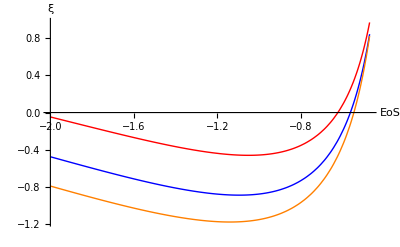

```mathematica
pltξvwICC=Plot[{ξICCfc[wICC],ξICCf1[wICC],ξICCf2[wICC]},{wICC,-2,-0.47},PlotStyle->{Blue,Orange,Red},AxesLabel->{"EoS","ξ"}]
```

Now we assume we do not have the observed Ωm0 data, how do this Ωm0 change the result. In other words, if the observed Ωm0 data float around some value, then how is the fitting result? We also consider the curvature.

```mathematica
fitξ2ICCManSum=Manipulate[numPlot["(",{ξICCffunc[Ωm0ICC,1-Ωm0ICC-Ωk0ICC,wICC,0.376],ξICCffunc[Ωm0ICC,1-Ωm0ICC-Ωk0ICC,wICC,0.426],ξICCffunc[Ωm0ICC,1-Ωm0ICC-Ωk0ICC,wICC,0.508]},")",{-1.5,1}],{{Ωm0ICC,0.274,"Matter Fraction"},0.1,0.9,Appearance->"Open"},{{Ωk0ICC,0,"Curvature"},-0.1,0.1,Appearance->"Open"},{{wICC,-1,"Equation of State"},-2,-0.47,Appearance->"Open"},Delimiter,Style["This is the fitting result of ξ from only transition redshift data.\n without the knowledge of Ωm0. "],Delimiter,Style["Slide to check how do EoS change this curve."],ControlPlacement->{Right},SaveDefinitions->Ture]
```

```mathematica
pltξvΩm0ICCManSum=Manipulate[Plot[{ξICCffunc[Ωm0ICC,1-Ωm0ICC-Ωk0ICC,wICC,0.426],ξICCffunc[Ωm0ICC,1-Ωm0ICC-Ωk0ICC,wICC,0.376],ξICCffunc[Ωm0ICC,1-Ωm0ICC-Ωk0ICC,wICC,0.508]},{Ωm0ICC,0.1,0.66},PlotStyle->{Blue,Orange,Red},AxesLabel->{"Ωm0","ξ"}],{{Ωk0ICC,0,"Curvature"},-0.1,0.1,Appearance->"Open"},{{wICC,-1,"Equation of State"},-2,-0.47,Appearance->"Open"},Delimiter,Style["Blue line is the center of ξ\n The other lines are the upper and lower value"],Delimiter,Style["Slide to check how do matter change this curve."],ControlPlacement->{Right},SaveDefinitions->Ture]
```

To summarize, taken the case that the universe is flat, and choose the parameters to be {w=-1}, the region for interaction constant ξ should be (-0.46, -1.28) with a center at -0.88, i.e., -0.88_-0.40^(+0.42) .

```mathematica
ztrrICC[0.358,-1,ξICC]==0.376
```

-1+0.179^(1/(-3+ξICC)) (-(1+(2 ξICC)/(-3+ξICC))/(-1-(0.358 ξICC)/(-3+ξICC)))^(1/(-3+ξICC))==0.376

```mathematica
ξICCrffunc[rICC_,wICC_,data_]:=ξICC/.FindRoot[ztrrICC[rICC,wICC,ξICC]==data,{ξICC,-0.6}]
```

```mathematica
ξICCrf2[wICC_]:=ξICCrffunc[0.398, wICC, 0.508]
```

```mathematica
ξICCrf1[wICC_]:=ξICCrffunc[0.358, wICC, 0.376]
```

Center

```mathematica
ξICCrfc[wICC_]:=ξICCrffunc[0.378, wICC, 0.426]
```

A example is ( w=-1 )

```mathematica
{ξICCrf1[-1],ξICCrfc[-1],ξICCrf2[-1]}
```

{-1.25282,-0.875189,-0.472561}

To summarize, taken the case that the universe is flat, and choose the parameters to be {w=-1}, the region for interation cosntant ξ should be (-1.25, -0.47) with a center at -0.88, i.e., -0.88_-0.37^(+0.41) .

This is a bit different from the result we got from Ωm0~ transition redshift plane. One possible reason is the second method doesn’t assume a flat universe, while the first one supposes the universe is flat.

In arXiv:0801.4233, a CPL parameterization of EoS and three-year WMAP data, SN Ia data, BAO gives a result of ξ~-0.02

#### Check consistancy

The consistancy between (Transition, Ωm0) plane fitting and (Transition, Ωm0/Ωd0) plane fitting is checked.
For a flat universe, r=Ωm0/(1-Ωm0). Solve out Ωm0, we get Ωm0=r/(1+r)(this is a monotonic function). Thus if we use the constrain that r∈(0.358, 0.398) with a center value 0.378, the value of Ωm0 is

```mathematica
{0.358/(1+0.358),0.378/(1+0.378),0.398/(1+0.398)}
```

{0.263623,0.274311,0.284692}

```mathematica
{ξICCffunc[0.263623,1-0.263623,-1,0.376],ξICCffunc[0.274310595065312,1-0.274310595065312,-1,0.426],ξICCffunc[0.28469241773962806,1-0.28469241773962806,-1,0.508]}
```

{-1.25282,-0.875189,-0.472561}

This result is exactly the same as the results from (Transition, r) plane.

### δ is constant + EoS w CPL

#### Definations and functions.

CPL EoS w=w0+w1 z/(1+z)

Useful relations.

```mathematica
hubblecmpintICCPL[w0_,w1_,ξICCPL_,z_]=Integrate[Exp[-3 w1/(1+tmp)](1+tmp)^(-3(w0+w1)-ξICCPL-1),{tmp,0,z},Assumptions->{tmp∈Reals&&z∈Reals&&z>-1}]
```

-ExpIntegralE[1-3 (w0+w1)-ξICCPL,3 w1]+(1/(1+z))^(3 (w0+w1)+ξICCPL) ExpIntegralE[1-3 (w0+w1)-ξICCPL,(3 w1)/(1+z)]

```mathematica
Re[hubblecmpintICCPL[-1,0.6,-0.2,10]]
```

14.1439

Fraction energy density

```mathematica
ΩmICCPL[Ωm0_,ξICCPL_,z_]:=Ωm0 (1+z)^(3-ξICCPL)
```

```mathematica
ΩdICCPL[Ωd0_,Ωm0_,w0_,w1_,ξICCPL_,z_]:=Ωm0 (1+z)^(3(1+w0+w1))Exp[3 w1/(1+z)]ξICCPL hubblecmpintICCPL[w0,w1,ξICCPL,z]+ Ωd0 (1+z)^(3(1+w0+w1))Exp[3 w1/(1+z)-3w1]//Simplify
```

Hubble function

```mathematica
hubbleICCPL[H0ICCPL_,Ωd0ICCPL_,Ωm0ICCPL_,w0ICCPL_,w1ICCPL_,ξICCPL_,z_]:=H0ICCPL √(ΩmICCPL[Ωm0ICCPL,ξICCPL,z]+ΩdICCPL[Ωd0ICCPL,Ωm0ICCPL,w0ICCPL,w1ICCPL,ξICCPL,z])
```

```mathematica
hubbleDICCPL[H0ICCPL_,Ωd0ICCPL_,Ωm0ICCPL_,w0ICCPL_,w1ICCPL_,ξICCPL_,z_]=D[hubbleICCPL[H0ICCPL,Ωd0ICCPL,Ωm0ICCPL,w0ICCPL,w1ICCPL,ξICCPL,z],z];
```

Deceleration parameter

```mathematica
qICCPL[H0ICCPL_,Ωd0ICCPL_,Ωm0ICCPL_,w0ICCPL_,w1ICCPL_,ξICCPL_,z_]:=-1+(1+z)/hubbleICCPL[H0ICCPL,Ωd0ICCPL,Ωm0ICCPL,w0ICCPL,w1ICCPL,ξICCPL,z] hubbleDICCPL[H0ICCPL,Ωd0ICCPL,Ωm0ICCPL,w0ICCPL,w1ICCPL,ξICCPL,z]
```

Check the definations and functions.

```mathematica
Re[hubbleDICCPL[H0w,Ωd0w,Ωm0w,-1,0.6,-0.02,10]]
```

188.13

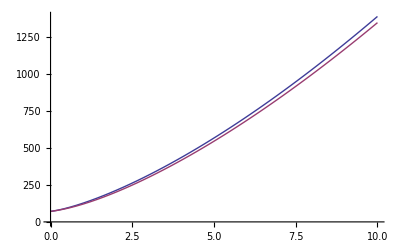

```mathematica
Plot[{hubbleICCPL[H0w,0.73,0.27,-1,0.6,-0.02,z],hubble[Ωm0w,Ωd0w,0,z]},{z,0,10}]
```

#### Plots, showcase, examinations

```mathematica
pldecICCPL[Ωm0ICCPL_,ξICCPL_,w0ICCPL_,w1ICCPL_,color_]:=Plot[Re[qICCPL[H0w,1-Ωm0ICCPL,Ωm0ICCPL,w0ICCPL,w1ICCPL,ξICCPL,z]],{z,-1,20},PlotRange->{{-1.05,20},{-1.05,1}},PlotStyle->color,AxesOrigin->{-1,0},AxesLabel->{z,q}];
```

Check the effects of different parameters.

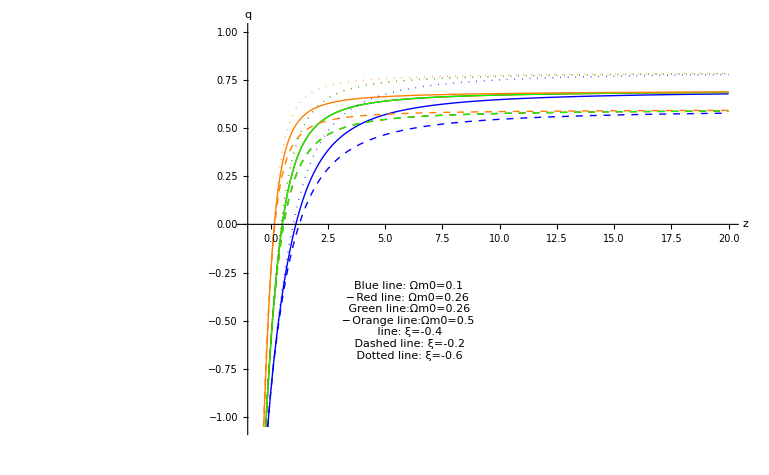

```mathematica
pldecICCPLShowSum=Show[{pldecICCPL[0.1,-0.4,-1.02,0.60,Blue],pldecICCPL[0.26,-0.4,-1.02,0.60,Red],pldecICCPL[0.26,-0.4,-1.02,0.60,Green],pldecICCPL[0.5,-0.4,-1.02,0.60,Orange],pldecICCPL[0.1,-0.2,-1.02,0.60,Directive[Blue,Dashed]],pldecICCPL[0.26,-0.2,-1.02,0.60,Directive[Red,Dashed]],pldecICCPL[0.26,-0.2,-1.02,0.60,Directive[Green,Dashed]],pldecICCPL[0.5,-0.2,-1.02,0.60,Directive[Orange,Dashed]],pldecICCPL[0.1,-0.6,-1.02,0.60,Directive[Blue,Dotted]],pldecICCPL[0.26,-0.6,-1.02,0.60,Directive[Red,Dotted]],pldecICCPL[0.26,-0.6,-1.02,0.60,Directive[Green,Dotted]],pldecICCPL[0.5,-0.6,-1.02,0.60,Directive[Orange,Dotted]]},Epilog->Inset[Framed[Style["Blue line: Ωm0=0.1\n─ Red line: Ωm0=0.26\n Green line:Ωm0=0.26\n─ Orange line:Ωm0=0.5\n line: ξ=-0.4\n Dashed line: ξ=-0.2\n Dotted line: ξ=-0.6",10],Background->LightYellow],{6,-0.5}]]
```

z->Infinity is a degenerate limit. For constant ξ and constant w models, this limit is determined by the interaction strength ξ . This might be useful if more complicated models are investigated and no large deviations are shown. [Nota]

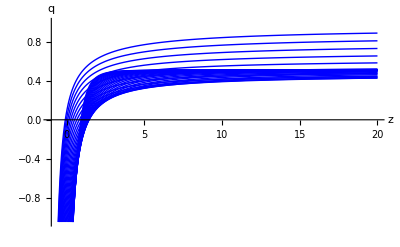
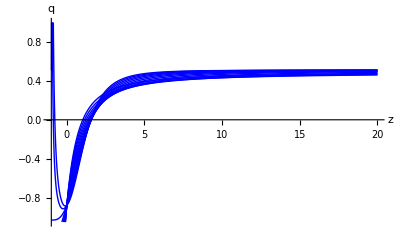
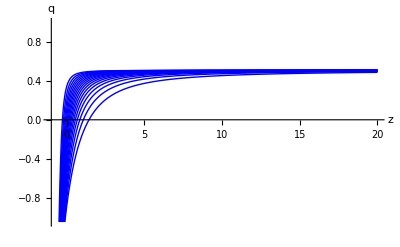
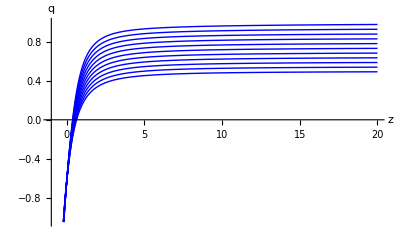
Varying CPL w0 | Varying CPL w1 | Varying Ωm0 | Varying ξ
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
varyingICCPLShowSum=Grid[{{"Varying CPL w0","Varying CPL w1","Varying Ωm0","Varying ξ"},Table[{Show[Table[pldecICCPL[0.1,-0.02,w0ICCPL,0.6,Blue],{w0ICCPL,-2,-0.3,0.05}]],Show[Table[pldecICCPL[0.1,-0.02,-1.02,w1ICCPL,Blue],{w1ICCPL,-0.2,1,0.1}]],Show[Table[pldecICCPL[Ωm0ICCPL,-0.02,-1.02,0.6,Blue],{Ωm0ICCPL,0.1,0.9,0.05}]],Show[Table[pldecICCPL[0.27,ξICCPL,-1.02,0.6,Blue],{ξICCPL,-1,0,0.1}]]}]},Frame->All]
```

Interaction ξ changes the limit, i.e., what value will it be at z->Infinity. EoS changes the the whole shape. Matter fraction also changes how fast q varies, but just in a small time scale.

Use movable slides to check how do the parameters affect the deceleration parameter. Just a toy.

```mathematica
pldecICCPLManSum=Manipulate[Show[{pldecICCPL[Ωm0ICCPL,ξICCPL,w0ICCPL,w1ICCPL,Orange],pldec[Ωm0ICCPL,{Pink,Thick}]}],{{Ωm0ICCPL,0.26,"Matter Fraction"},0,1,Appearance->"Open"},{{ξICCPL,-0.4,"Interaction"},-1,0,Appearance->"Open"},{{w0ICCPL,-1.02,"CPL EoS w0"},-2,-0.3,Appearance->"Open"},{{w1ICCPL,0.6,"CPL EoS w1"},-0.2,1,Appearance->"Open"},Delimiter,Style["Pink is the deceleration parameter for LCDM.",Medium],Style["Orange is for interacting CPL model with Q=ξ H ρ_m",Medium],ControlPlacement->{Right,Right,Right},SaveDefinitions->True]
```

#### Transition redshift

Find out the expression for transition redshift

```mathematica
ztrICCPL[Ωm0ICCPL_,Ωd0ICCPL_,ξICCPL_,w0ICCPL_,w1ICCPL_]:=Re[z/.FindRoot[(1+3(w0ICCPL+w1ICCPL z/(1+z)))ΩdICCPL[Ωd0ICCPL,Ωm0ICCPL,w0ICCPL,w1ICCPL,ξICCPL,z]+ΩmICCPL[Ωm0ICCPL,ξICCPL,z]==0,{z,0}]]
```

Define rICC=Ωm0ICC/Ωd0ICC

```mathematica
ΩmrICCPL[rICCPL_,ξICCPL_,z_]:=rICCPL (1+z)^(3-ξICCPL)
```

```mathematica
ΩdrICCPL[rICCPL_,w0ICCPL_,w1ICCPL_,ξICCPL_,z_]:=rICCPL (1+z)^(3(1+w0ICCPL+w1ICCPL))Exp[3 w1ICCPL/(1+z)]ξICCPL hubblecmpintICCPL[w0ICCPL,w1ICCPL,ξICCPL,z]+ (1+z)^(3(1+w0ICCPL+w1ICCPL))Exp[3 w1ICCPL/(1+z)-3w1ICCPL]//Simplify
```

```mathematica
ztrrICCPL[rICCPL_,ξICCPL_,w0ICCPL_,w1ICCPL_]:=Re[z/.FindRoot[(1+3(w0ICCPL+w1ICCPL z/(1+z)))ΩdrICCPL[rICCPL,w0ICCPL,w1ICCPL,ξICCPL,z]+ΩmrICCPL[rICCPL,ξICCPL,z]==0,{z,0}]]
```

Test this.

```mathematica
ztrrICCPL[0.5,-0.02,-1,0.6]
```

0.46757

#### Visualization of transition redshift.

Check the behavior of this transition redshift.

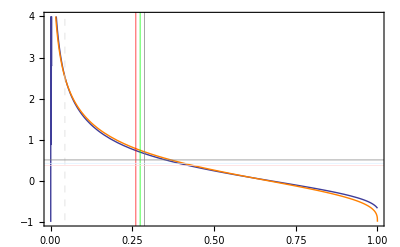

```mathematica
pldecrICCPL=Plot[{ztrICCPL[Ωm0ICCPL,1-Ωm0ICCPL,-0.02,-1.02,0.2],ztr[Ωm0ICCPL,1-Ωm0ICCPL]},{Ωm0ICCPL,0,1},PlotRange->{{0,1},{-1,4}},PlotStyle->{Thick,Orange},AxesOrigin->{0,-1},Frame->True,GridLines->{{{0.044,Dashed},{0.261,Red},{0.274,Green},{0.287,Gray}},{{0.376,LightRed},{0.426,LightBlue},{0.508,Gray}}},PlotLegend->{"Q=-0.02 H ρ_c","LCDM"},LegendPosition->{1.1,-0.4}]
```

```mathematica
plztrICCPL[ξICCPL_,w0ICCPL_,w1ICCPL_,color_]:=Plot[ztrICCPL[Ωm0ICCPL,1-Ωm0ICCPL,ξICCPL,w0ICCPL,w1ICCPL],{Ωm0ICCPL,0,1},PlotRange->{{0,1},{-1,4}},PlotStyle->color,AxesOrigin->{0,-1}];
```

```mathematica
plztrICCPLManSum=Manipulate[Show[{plztrICCPL[ξICCPL,w0ICCPL,w1ICCPL,Orange],Plot[ztr[Ωm0ICCPL,1-Ωm0ICCPL],{Ωm0ICCPL,0,1},PlotRange->{{0,1},{-1,4}},PlotStyle->Pink,AxesOrigin->{0,-1}]}],{{ξICCPL,-0.4,"Interaction"},-1,0,Appearance->"Open"},{{w0ICCPL,-1.02,"CPL EoS w0"},-2,-0.3,Appearance->"Open"},{{w1ICCPL,0.6,"CPL EoS w1"},-0.2,1,Appearance->"Open"},Delimiter,Style["Orange is for interacting CPL model with Q=ξ H ρ_m",Medium],ControlPlacement->{Right,Right,Right},SaveDefinitions->True]
```

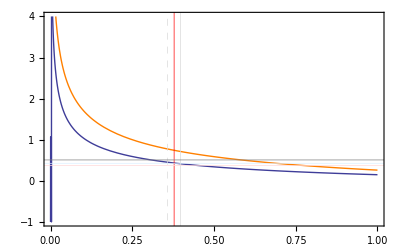

```mathematica
pldecrICCPL=Plot[{ztrrICCPL[rICCPL,-0.6,-1.02,0.6],ztrr[rICCPL]},{rICCPL,0,1},PlotRange->{{0,1},{-1,4}},PlotStyle->{Thick,Orange},AxesOrigin->{0,-1},Frame->True,GridLines->{{{0.358,Dashed},{0.378,Directive[Red]},0.398},{{0.376,LightRed},{0.426,LightBlue},{0.508,Gray}}},PlotLegend->{"CPL,Q=-0.6 H ρ_c","LCDM"},LegendPosition->{1.1,-0.4}]
```

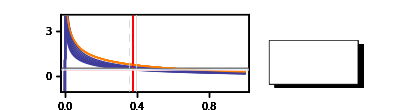

```mathematica
pldecrICCPLDense=Show[Table[pldecr=Plot[{ztrrICCPL[rICCPL,ξICCPL,-1.02,0.6],ztrr[rICCPL]},{rICCPL,0,1},PlotRange->{{0,1},{-1,4}},PlotStyle->{Thick,Orange},AxesOrigin->{0,-1},Frame->True,GridLines->{{{0.358,Dashed},{0.378,Directive[Red]},0.398},{{0.376,LightRed},{0.426,LightBlue},{0.508,Gray}}},PlotLegend->{"CPL,Q=ξ H ρ_c,\n with ξ∈(-0.8,0) step=0.1","LCDM"},LegendPosition->{1.1,-0.4}],{ξICCPL,-0.8,0,0.1}]]
```

#### Find out allowed region of interactions.

To find out the region of ξ, set w=-1 and Ωd0=1-Ωm0. Let the ztr-Ωm0 line cross points (0.287,0.508) and (0.261, 0.376).

```mathematica
ztrICCPL[Ωm0ICCPL_,Ωd0ICCPL_,ξICCPL_,w0ICCPL_,w1ICCPL_]
```

FindRoot::nlnum: The function value {1.^3.  - 1.\ ξICCPL_\ Ωm0ICCPL_ + 1.\ (1.  + 3.\ (0.  + w0ICCPL_))\ (Ωd0ICCPL_ - 1.\ 2.71828^3.\ Pattern[« 2 »]\ (ExpIntegralE[Plus[« 3 »], Times[« 2 »]] - 1.\ Power[« 2 »]\ ExpIntegralE[« 2 »])\ ξICCPL_\ Ωm0ICCPL_)}
 is not a list of numbers with dimensions {1} at {z} = {0.}.

ReplaceAll::reps: {FindRoot[(1 + 3\ Plus[« 2 »])\ ΩdICCPL[Ωd0ICCPL_, Ωm0ICCPL_, w0ICCPL_, w1ICCPL_, ξICCPL_, z] + ΩmICCPL[Ωm0ICCPL_, ξICCPL_, z] == 0, {z, 0}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Re[z/.FindRoot[(1+3 (w0ICCPL_+(w1ICCPL_ z)/(1+z))) ΩdICCPL[Ωd0ICCPL_,Ωm0ICCPL_,w0ICCPL_,w1ICCPL_,ξICCPL_,z]+ΩmICCPL[Ωm0ICCPL_,ξICCPL_,z]==0,{z,0}]]

```mathematica
(* ztrICCPL[0.287,1-0.287,ξICCPL1,-1.02,0.6]==0.508 *)
```

```mathematica
FindRoot[ztrICCPL[0.287,1-0.287,ξICCPL1,-1.02,0.6]==0.508,{ξICCPL1,-0.6}]
```

FindRoot::nlnum: The function value {0.287\ 1.^3.  - 1.\ ξICCPL1 - 12.4623\ (0.117858  - 0.287\ ξICCPL1\ ExpIntegralE[2.26  + Times[« 2 »], 1.8] + 0.287\ 1.^-1.26 + ξICCPL1\ ξICCPL1\ ExpIntegralE[2.26  + Times[« 2 »], 1.8])}
 is not a list of numbers with dimensions {1} at {z} = {0.}.

ReplaceAll::reps: {FindRoot[(1 + 3\ Plus[« 2 »])\ ΩdICCPL[0.713, 0.287, -1.02, 0.6, ξICCPL1, z] + ΩmICCPL[0.287, ξICCPL1, z] == 0, {z, 0}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{ξICCPL1→-0.213119}

```mathematica
FindRoot[ztrICCPL[0.261,1-0.261,ξICCPL1,-1.02,0.6]==0.376,{ξICCPL1,-0.6}]
```

FindRoot::nlnum: The function value {0.261\ 1.^3.  - 1.\ ξICCPL1 - 12.4623\ (0.122156  - 0.261\ ξICCPL1\ ExpIntegralE[2.26  + Times[« 2 »], 1.8] + 0.261\ 1.^-1.26 + ξICCPL1\ ξICCPL1\ ExpIntegralE[2.26  + Times[« 2 »], 1.8])}
 is not a list of numbers with dimensions {1} at {z} = {0.}.

ReplaceAll::reps: {FindRoot[(1 + 3\ Plus[« 2 »])\ ΩdICCPL[0.739, 0.261, -1.02, 0.6, ξICCPL1, z] + ΩmICCPL[0.261, ξICCPL1, z] == 0, {z, 0}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{ξICCPL1→-1.03882}

Cross the Center of best fit. (0.274,0.426)

```mathematica
FindRoot[ztrICCPL[0.274,1-0.274,ξICCPL1,-1.02,0.6]==0.426,{ξICCPL1,-0.6}]
```

FindRoot::nlnum: The function value {0.274\ 1.^3.  - 1.\ ξICCPL1 - 12.4623\ (0.120007  - 0.274\ ξICCPL1\ ExpIntegralE[2.26  + Times[« 2 »], 1.8] + 0.274\ 1.^-1.26 + ξICCPL1\ ξICCPL1\ ExpIntegralE[2.26  + Times[« 2 »], 1.8])}
 is not a list of numbers with dimensions {1} at {z} = {0.}.

ReplaceAll::reps: {FindRoot[(1 + 3\ Plus[« 2 »])\ ΩdICCPL[0.726, 0.274, -1.02, 0.6, ξICCPL1, z] + ΩmICCPL[0.274, ξICCPL1, z] == 0, {z, 0}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{ξICCPL1→-0.635668}

To summarize, taken the case that the universe is flat, and choose the parameters to be {w0=-1.02,w1=0.6}, the region for interaction constant ξ should be (-1.04,-0.21) with a center at -0.64, i.e., -0.64_-0.40^(+0.42) .

```mathematica
ztrICCPL[0.358,ξICCPL]==0.376
```

ztrICCPL[0.358,ξICCPL]==0.376

```mathematica
FindRoot[ztrrICCPL[0.358,ξICC,-1.02,0.6]==0.376,{ξICC,-1}]
```

FindRoot::nlnum: The function value {0.358\ 1.^3.  - 1.\ ξICC - 12.4623\ (0.165299  - 0.358\ ξICC\ ExpIntegralE[2.26  + Times[« 2 »], 1.8] + 0.358\ 1.^-1.26 + ξICC\ ξICC\ ExpIntegralE[2.26  + Times[« 2 »], 1.8])}
 is not a list of numbers with dimensions {1} at {z} = {0.}.

ReplaceAll::reps: {FindRoot[(1 + 3\ Plus[« 2 »])\ ΩdrICCPL[0.358, -1.02, 0.6, ξICC, z] + ΩmrICCPL[0.358, ξICC, z] == 0, {z, 0}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{ξICC→-1.01249}

```mathematica
FindRoot[ztrrICCPL[0.398,ξICC,-1.02,0.6]==0.508,{ξICC,-0.6}]
```

FindRoot::nlnum: The function value {0.398\ 1.^3.  - 1.\ ξICC - 12.4623\ (0.165299  - 0.398\ ξICC\ ExpIntegralE[2.26  + Times[« 2 »], 1.8] + 0.398\ 1.^-1.26 + ξICC\ ξICC\ ExpIntegralE[2.26  + Times[« 2 »], 1.8])}
 is not a list of numbers with dimensions {1} at {z} = {0.}.

ReplaceAll::reps: {FindRoot[(1 + 3\ Plus[« 2 »])\ ΩdrICCPL[0.398, -1.02, 0.6, ξICC, z] + ΩmrICCPL[0.398, ξICC, z] == 0, {z, 0}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{ξICC→-0.228688}

Center of best fit.

```mathematica
FindRoot[ztrrICCPL[0.378,ξICC,-1.02,0.6]==0.426,{ξICC,-1}]
```

FindRoot::nlnum: The function value {0.378\ 1.^3.  - 1.\ ξICC - 12.4623\ (0.165299  - 0.378\ ξICC\ ExpIntegralE[2.26  + Times[« 2 »], 1.8] + 0.378\ 1.^-1.26 + ξICC\ ξICC\ ExpIntegralE[2.26  + Times[« 2 »], 1.8])}
 is not a list of numbers with dimensions {1} at {z} = {0.}.

ReplaceAll::reps: {FindRoot[(1 + 3\ Plus[« 2 »])\ ΩdrICCPL[0.378, -1.02, 0.6, ξICC, z] + ΩmrICCPL[0.378, ξICC, z] == 0, {z, 0}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{ξICC→-0.633048}

To summarize, taken the case that the universe is flat, and choose the parameters to be  {w0=-1.02,w1=0.6}, the region for interation cosntant ξ should be (-1.01, -0.23) with a center at -0.63, i.e., -0.63_-0.38^(+0.40) .

In arXiv:0801.4233, a CPL parameterization of EoS and three-year WMAP data, SN Ia data, BAO gives a result of ξ~-0.02 
We can see from

### ---------------------------------------------------------------------------------------------------------------------------------------------------------------------------------

### Take the form Q_c=ξ H ρ_d. I2 model

Hubble function without curvature

```mathematica
hubbleI2CC[H0_,Ωd0_,Ωm0_,w_,ξ_,z_]:=H0 √(Ωm+Ωd);
```

Conventions:
parameters : H0, Ωm0, Ωd0, w, ξ, z.

### Constant ξ + Constant w. I2CC model.

#### Definations

Fraction energy density

```mathematica
ΩmI2CC[Ωm0I2CC_,Ωd0I2CC_,wI2CC_,ξI2CC_,z_]:=(Ωm0I2CC +ξI2CC/(ξI2CC+3wI2CC))(1+z)^3+-ξI2CC/(ξI2CC+3wI2CC)ΩdI2CC[Ωd0I2CC,wI2CC,ξI2CC,z]
```

```mathematica
ΩdI2CC[Ωd0I2CC_,wI2CC_,ξI2CC_,z_]:=Ωd0I2CC (1+z)^(3(1+wI2CC)+ξI2CC)
```

Hubble function

```mathematica
hubbleI2CC[H0I2CC_,Ωm0I2CC_,Ωd0I2CC_,wI2CC_,ξI2CC_,z_]=H0I2CC √(ΩmI2CC[Ωm0I2CC,Ωd0I2CC,wI2CC,ξI2CC,z]+ΩdI2CC[Ωd0I2CC,wI2CC,ξI2CC,z])
```

H0I2CC √((1+z)^(3 (1+wI2CC)+ξI2CC) Ωd0I2CC-((1+z)^(3 (1+wI2CC)+ξI2CC) ξI2CC Ωd0I2CC)/(3 wI2CC+ξI2CC)+(1+z)^3 (ξI2CC/(3 wI2CC+ξI2CC)+Ωm0I2CC))

Deceleration parameter

```mathematica
qI2CC[H0I2CC_,Ωm0I2CC_,Ωd0I2CC_,wI2CC_,ξI2CC_,z_]=-1+(1+z)/hubbleI2CC[H0I2CC,Ωm0I2CC,Ωd0I2CC,wI2CC,ξI2CC,z] D[hubbleI2CC[H0I2CC,Ωm0I2CC,Ωd0I2CC,wI2CC,ξI2CC,z],z];
```

```mathematica
qI2CC[H0I2CC,Ωm0I2CC,Ωd0I2CC,wI2CC,ξI2CC,z]//FullSimplify
```

(ξI2CC+3 wI2CC (1+z)^(3 wI2CC+ξI2CC) (1+3 wI2CC+ξI2CC) Ωd0I2CC+3 wI2CC Ωm0I2CC+ξI2CC Ωm0I2CC)/(2 (ξI2CC (1+Ωm0I2CC)+3 wI2CC ((1+z)^(3 wI2CC+ξI2CC) Ωd0I2CC+Ωm0I2CC)))

```mathematica
Limit[qI2CC[H0I2CC,Ωm0I2CC,Ωd0I2CC,wI2CC,ξI2CC,z]//FullSimplify,z->Infinity,Assumptions->(3 wI2CC+ξI2CC)<0]
```

1/2

At z-> Infinity limit, deceleration parameter→ 1/2, with 3 wICC+ξICC<0. This is different from LCDM model.

#### Plots, showcase, manipulate toys

```mathematica
pldecI2CC[Ωm0I2CC_,wI2CC_,ξI2CC_,color_]:=Plot[qI2CC[H0w,Ωm0I2CC,1-Ωm0I2CC,wI2CC,ξI2CC,z],{z,-1,10},PlotRange->{{-1.05,10},{-1.05,1}},PlotStyle->color,AxesOrigin->{-1,0},AxesLabel->{z,q}];
```

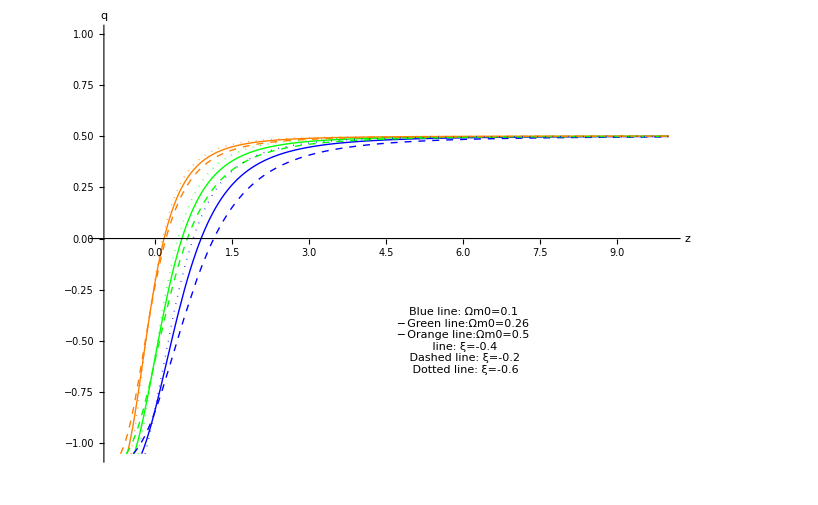

```mathematica
pldecI2CCShowSum=Show[{pldecI2CC[0.1,-1,-0.4,Blue],pldecI2CC[0.26,-1,-0.4,Green],pldecI2CC[0.5,-1,-0.4,Orange],pldecI2CC[0.1,-1,-0.2,Directive[Blue,Dashed]],pldecI2CC[0.26,-1,-0.2,Directive[Green,Dashed]],pldecI2CC[0.5,-1,-0.2,Directive[Orange,Dashed]],pldecI2CC[0.1,-1,-0.6,Directive[Blue,Dotted]],pldecI2CC[0.26,-1,-0.6,Directive[Green,Dotted]],pldecI2CC[0.5,-1,-0.6,Directive[Orange,Dotted]]},Epilog->Inset[Framed[Style["Blue line: Ωm0=0.1\n─ Green line:Ωm0=0.26\n─ Orange line:Ωm0=0.5\n line: ξ=-0.4\n Dashed line: ξ=-0.2\n Dotted line: ξ=-0.6",10],Background->LightYellow],{6,-0.5}]]
```

z->Infinity is a degenerate limit. For constant ξ and constant w models, this limit is determined by the interaction strength ξ . This might be useful if more complicated models are investigated and no large deviations are shown. [Nota]

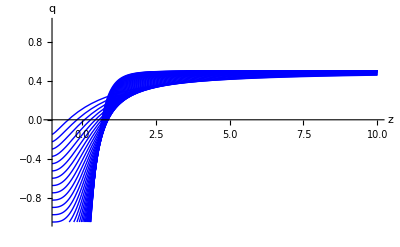
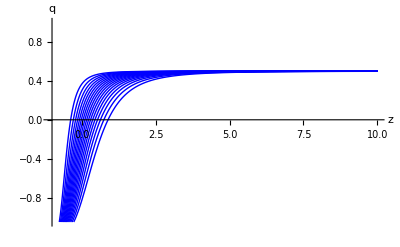
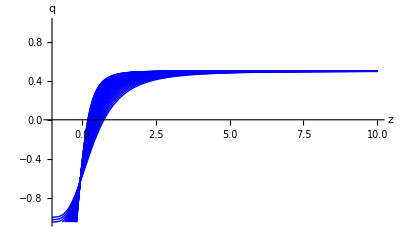
Varying EoS | Varying Ωm0 | Varying ξ
-Graphics- | -Graphics- | -Graphics-

```mathematica
varyingI2CCShowSum=Grid[{{"Varying EoS","Varying Ωm0","Varying ξ"},Table[{Show[Table[pldecI2CC[0.1,wI2CC,-0.4,Blue],{wI2CC,-2,-0.3,0.05}]],Show[Table[pldecI2CC[Ωm0I2CC,-1,-0.4,Blue],{Ωm0I2CC,0.1,0.9,0.05}]],Show[Table[pldecI2CC[0.27,-1,ξI2CC,Blue],{ξI2CC,-2,0,0.05}]]}]},Frame->All]
```

Use movable slides to check how do the parameters affect the deceleration parameter. Just a toy.

```mathematica
pldecI2CCManSum=Manipulate[Show[{pldecI2CC[Ωm0I2CC,wI2CC,ξI2CC,Orange],pldec[Ωm0I2CC,{Pink,Thick}]}],{{Ωm0I2CC,0.26,"Matter Fraction"},0,1,Appearance->"Open"},{{ξI2CC,-0.4,"Interaction"},-1,0,Appearance->"Open"},{{wI2CC,-1,"Equation of State"},-1.5,-0.5,Appearance->"Open"},Delimiter,Style["Pink is the deceleration parameter for LCDM.",Medium],Style["Orange is for interacting model with Q=ξ H ρ_m",Medium],ControlPlacement->{Right,Right,Right},SaveDefinitions->True]
```

#### Transition redshift definations and equations.

Find out the expression for transition redshift

```mathematica
ΩmI2CC[Ωm0I2CC_,Ωd0I2CC_,wI2CC_,ξI2CC_,z_]:=(Ωm0I2CC +ξI2CC/(ξI2CC+3wI2CC))(1+z)^3+-ξI2CC/(ξI2CC+3wI2CC)ΩdI2CC[Ωd0I2CC,wI2CC,ξI2CC,z]
```

```mathematica
ΩdI2CC[Ωd0I2CC_,wI2CC_,ξI2CC_,z_]:=Ωd0I2CC (1+z)^(3(1+wI2CC)+ξI2CC)
```

```mathematica
(3wI2CC+1)ΩdI2CC[Ωd0I2CC,wI2CC,ξI2CC,z]+ΩmI2CC[Ωm0I2CC,Ωd0I2CC,wI2CC,ξI2CC,z]==0//Simplify
```

1/(3 wI2CC+ξI2CC)(1+z) (ξI2CC (1+3 wI2CC (1+z)^(3 wI2CC+ξI2CC) Ωd0I2CC+Ωm0I2CC)+3 wI2CC ((1+3 wI2CC) (1+z)^(3 wI2CC+ξI2CC) Ωd0I2CC+Ωm0I2CC))==0

```mathematica
ztrI2CC[Ωm0I2CC_,Ωd0I2CC_,wI2CC_,ξI2CC_]=-1+(((3wI2CC+ξI2CC)Ωm0I2CC+ξI2CC Ωd0I2CC)/(-3wI2CC(3wI2CC+ξI2CC+1)Ωd0I2CC))^(1/(3wI2CC+ξI2CC))
```

-1+3^(-1/(3 wI2CC+ξI2CC)) (-(ξI2CC Ωd0I2CC+(3 wI2CC+ξI2CC) Ωm0I2CC)/(wI2CC (1+3 wI2CC+ξI2CC) Ωd0I2CC))^(1/(3 wI2CC+ξI2CC))

```mathematica
ztrI2CC[0.27,0.73,-1,-0.4]
```

0.540312

The first solution is trivil. So the second one is taken.

Define rICC=Ωm0ICC/Ωd0ICC

```mathematica
ztrrI2CC[rI2CC_,wI2CC_,ξI2CC_]=-1+(((3wI2CC+ξI2CC)rI2CC+ξI2CC)/(-3wI2CC(3wI2CC+ξI2CC+1)))^(1/(3 wI2CC+ξI2CC));
```

#### Visualiztion of transition redshift

Check the behavior of this transition redshift.

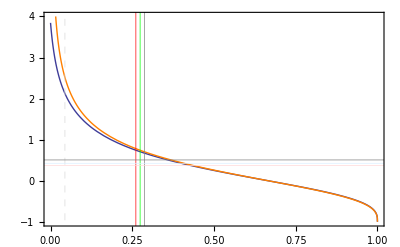

```mathematica
pldecrI2CC=Plot[{ztrI2CC[Ωm0I2CC,1-Ωm0I2CC,-1,-0.05],ztr[Ωm0I2CC,1-Ωm0I2CC]},{Ωm0I2CC,0,1},PlotRange->{{0,1},{-1,4}},PlotStyle->{Thick,Orange},AxesOrigin->{0,-1},Frame->True,GridLines->{{{0.044,Dashed},{0.261,Red},{0.274,Green},{0.287,Gray}},{{0.376,LightRed},{0.426,LightBlue},{0.508,Gray}}},PlotLegend->{"Q=-0.05 H ρ_c","LCDM"},LegendPosition->{1.1,-0.4}]
```

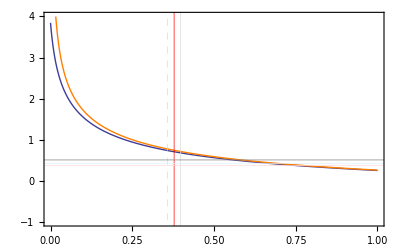

```mathematica
pldecrrI2CC=Plot[{ztrrI2CC[rI2CC,-1,-0.05],ztrr[rI2CC]},{rI2CC,0,1},PlotRange->{{0,1},{-1,4}},PlotStyle->{Thick,Orange},AxesOrigin->{0,-1},Frame->True,GridLines->{{{0.358,Dashed},{0.378,Directive[Red]},0.398},{{0.376,LightRed},{0.426,LightBlue},{0.508,Gray}}},PlotLegend->{"Q=-0.05 H ρ_c","LCDM"},LegendPosition->{1.1,-0.4}]
```

```mathematica
plztrI2CC[wI2CC_,ξI2CC_,color_]:=Plot[ztrI2CC[Ωm0I2CC,1-Ωm0I2CC,wI2CC,ξI2CC],{Ωm0I2CC,0,1},PlotRange->{{0,1},{-1,4}},PlotStyle->color,AxesOrigin->{0,-1},AxesLabel->{"Ωm0","z_t"}];
```

```mathematica
plztrI2CCManSum=Manipulate[Show[{plztrI2CC[wI2CC,ξI2CC,Orange],Plot[ztr[Ωm0I2CC,1-Ωm0I2CC],{Ωm0I2CC,0,1},PlotRange->{{0,1},{-1,4}},PlotStyle->Pink,AxesOrigin->{0,-1}]}],{{ξI2CC,-0.4,"Interaction"},-1,0,Appearance->"Open"},{{wI2CC,-1.02,"Equation of state"},-2,-0.3,Appearance->"Open"},Delimiter,Style["Pink is the transition redshift vs Ωm0 for LCDM.",Medium],Style["Orange is for interacting model with Q=ξ H ρ_d,",Medium],Style["where ξ is constant and EoS is constant",Medium],ControlPlacement->{Right,Right,Right},SaveDefinitions->True]
```

#### Find out the allowed region of coupling constant.

To find out the region of ξ, set w=-1 and Ωd0=1-Ωm0. Let the ztr-Ωm0 line cross points (0.287,0.508) and (0.261, 0.376).

```mathematica
ztrI2CC[0.287,1-0.287,-1,ξI2CC1]==0.508
```

-1+0.467508^(1/(-3+ξI2CC1)) ((0.287 (-3+ξI2CC1)+0.713 ξI2CC1)/(-2+ξI2CC1))^(1/(-3+ξI2CC1))==0.508

```mathematica
FindRoot[ztrI2CC[0.287,1-0.287,-1,ξI2CC1]==0.508,{ξI2CC1,-0.6}]
```

{ξI2CC1→-0.409217}

```mathematica
FindRoot[ztrI2CC[0.261,1-0.261,-1,ξI2CC1]==0.376,{ξI2CC1,-0.6}]
```

{ξI2CC1→-1.07368}

Cross the Center of best fit. (0.274,0.426)

```mathematica
FindRoot[ztrI2CC[0.274,1-0.274,-1,ξI2CC1]==0.426,{ξI2CC1,-0.6}]
```

{ξI2CC1→-0.760999}

To summarize, taken the case that the universe is flat, and choose the parameters to be {w=-1}, the region for interaction constant ξ should be (-1.07,-0.41) with a center at -0.76, i.e., -0.76_-0.31^(+0.35) .

```mathematica
ztrrI2CC[0.358,-1,ξI2CC]==0.376
```

-1+3^(-1/(-3+ξI2CC)) ((0.358 (-3+ξI2CC)+ξI2CC)/(-2+ξI2CC))^(1/(-3+ξI2CC))==0.376

```mathematica
FindRoot[ztrrI2CC[0.358,-1,ξI2CC]==0.376,{ξI2CC,-1}]
```

{ξI2CC→-1.05903}

```mathematica
FindRoot[ztrrI2CC[0.398,-1,ξI2CC]==0.508,{ξI2CC,-0.6}]
```

{ξI2CC→-0.420298}

Center of best fit.

```mathematica
FindRoot[ztrrI2CC[0.378,-1,ξI2CC]==0.426,{ξI2CC,-1}]
```

{ξI2CC→-0.759371}

To summarize, taken the case that the universe is flat, and choose the parameters to be {w=-1}, the region for interation cosntant ξ should be ( -1.06,-0.42) with a center at -0.76, i.e., -0.76_-0.30^(+0.34) .

This is a bit different from the result we got from Ωm0~ transition redshift plane. One possible reason is the second method doesn’t assume a flat universe, while the first one supposes the universe is flat.

In arXiv:0801.4233, a CPL parameterization of EoS and three-year WMAP data, SN Ia data, BAO gives a result of ξ~-0.04

## Summary

### Interacting models

#### List of what to make clear

[Quantitively] Fixed Ωm0, the allowed ξ with a changing of EoS.

[Quantitively] Fixed ω, the allowed ξ with a change Ωm0 or r.

[Quantitively] ξ is minus means energy transfer to dark matter, which delays the appearence of dark energy dominated era. What is the result of this method.

[Quantitively] CPL parameterization can be categoried into 3 cases. Check their effects on the fitting. How do different category change the ξ fitting results.

Phantom

Quintessence

Crossing -1

[Quantitively] The effect of Ωm0 in different CPL parameterizations.

#### BASIC

Evolution of energy density for Q_c=ξ H ρ_c, constant ξ, constant w, and ξ≠-3w

Ωm=Ωm0 (1+z)^(3-ξ)

Ωd=(Ωd0+ξ/(3w+ξ)Ωm0)(1+z)^(3(1+w))+-ξ/(3w+ξ)Ωm≡Ωd0'(1+z)^(3(1+w))+-ξ/(3w+ξ)Ωm

Evolution of energy density for Q_c=ξ H ρ_d, constant ξ, constant w, and ξ≠-3w

Ωm=(Ωm0+ξ/(ξ+3w)Ωd0)(1+z)^3+-ξ/(ξ+3w)Ωd≡Ωm0'(1+z)^3+-ξ/(ξ+3w)Ωd

Ωd=Ωd0(1+z)^(3(1+w)+ξ)

So in the two cases, coupling constant has two effects

Amplifies the curve of deceleration parameter.

Energy flow between DE and DM.

### Interacting model Q_c=ξ H ρ_c with constant ξ and constant EoS w.

Derived from (transition redshift, Ωm0) plane, the allowed region for coupling constant ξ is  (-1.28, -0.46) with a center at -0.88, i.e., -0.88_-0.40^(+0.42),  taken the case that the universe is flat, and choose the EoS parameter {w=-1}.
Derived from the (transition redshift, Ωm0/Ωd0) plane, the allowed region of coupling constant ξ is  (-1.25,- 0.47) with a center at -0.88, i.e., -0.88_-0.37^(+0.41) .
There is a bit difference between the two answers. One possible reason is the second method doesn’t assume a flat universe, while the first one supposes the universe is flat.

To check the constancy of the two methods,

The plots of deceleration parameter are shown below. At the limit z->Infinity, the deceleration parameter is degenerate for different Ωm0 in this constant ξ and constant w model. 
Theoretically, this limit is determined by the interaction strength ξ, which is (1-ξ)/2, with 3w+ξ<0.

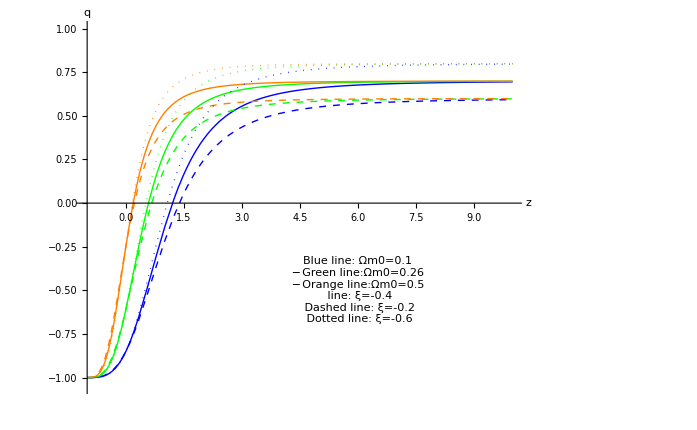

```mathematica
pldecICCShowSum
```

To check the effect of different parameters, another plot is shown. Interaction ξ changes the value of deceleration parameter at z→ ∞ limit. EoS changes the the whole shape. Matter fraction determines how fast q varies, but just in a small time scale.

```mathematica
varyingICCShowSum
```

Varying EoS | Varying Ωm0 | Varying ξ
-Graphics- | -Graphics- | -Graphics-

A toy to play with is also provied

```mathematica
pldecICCManSum
```

A toy of transition redshift

```mathematica
plztrICCManSum
```

The fitting results of coupling constant ξ is

```mathematica
fitξICCManSum
```

For different constant EoS, the fitting results using Ωm0∈(0.61,0.287) with a center value 0.274 and Transition redshift ∈ (0.376,0.508) with a center value 0.426. When EoS is very small, the line cross zero. But that is not so useful.

```mathematica
pltξvwICC
```

-Graphics-

Now we assume we do not have the observed Ωm0 data, how do this Ωm0 change the result. In other words, if the observed Ωm0 data float around some value, then how is the fitting result? We also consider the curvature.

Why is there a point that the three lines converge????????

```mathematica
pltξΩm0ICCManSum
```

In addition, we can also find out the effects of Curvature, EoS. Assuming we have a constrain of Transition redshift (0.376,0.508) with a center at 0.426.

```mathematica
fitξ2ICCManSum
```

### Interacting model Q_c=ξ H ρ_d with constant ξ and constant EoS w.

Derived from (transition redshift, Ωm0) plane, the allowed region for coupling constant ξ is ( -1.06,-0.42) with a center at -0.76, i.e., -0.76_-0.30^(+0.34) ,  taken the case that the universe is flat, and choose the EoS parameter {w=-1}.
Derived from the (transition redshift, Ωm0/Ωd0) plane, the allowed region of coupling constant ξ is (-1.07,-0.41) with a center at -0.76, i.e., -0.76_-0.31^(+0.35).

The plots of deceleration parameter are shown below. At the limit z->Infinity, the deceleration parameter ALL goes to 1/2.
Theoretically, this limit is  1/2 which is not related to any parameters, with 3w+ξ<0.

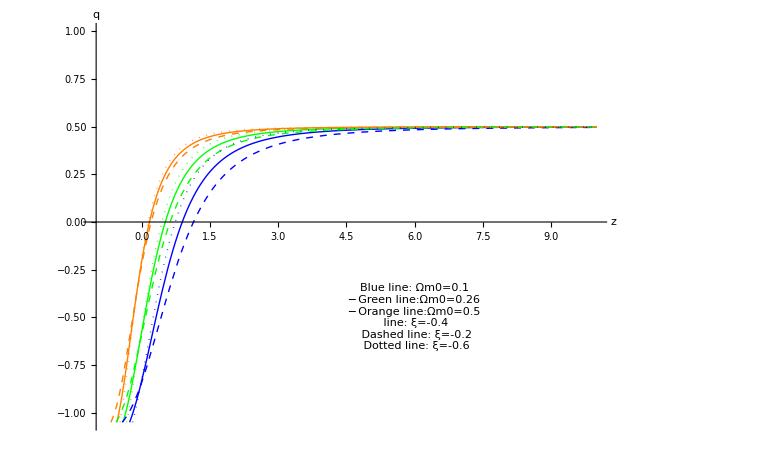

```mathematica
pldecI2CCShowSum
```

To check the effect of different parameters, another plot is shown.

```mathematica
varyingI2CCShowSum
```

Varying EoS | Varying Ωm0 | Varying ξ
-Graphics- | -Graphics- | -Graphics-

A toy to play with is also provied

```mathematica
pldecI2CCManSum
```

A toy of transition redshift

```mathematica
plztrI2CCManSum
```

### Interacting model with constant ξ and CPL parameterized EoS w=w0+w1 z/(1+z).

For a flat universe, choose the parameters {w0=-1.02,w1=0.6}, the region for interation cosntant ξ should be  (-1.04,-0.21) with a center at -0.64, i.e., -0.64_-0.40^(+0.42) ,derived from the (transition redshift, Ωm0) plane, while a result of (-1.01, -0.23) with a center at -0.63, i.e., -0.63_-0.38^(+0.40) , derived from (transition redshift, Ωm0/Ωd0) plane.

Deceleration parameter is shown below. Behaves similiar to the constant ξ constant w situation.

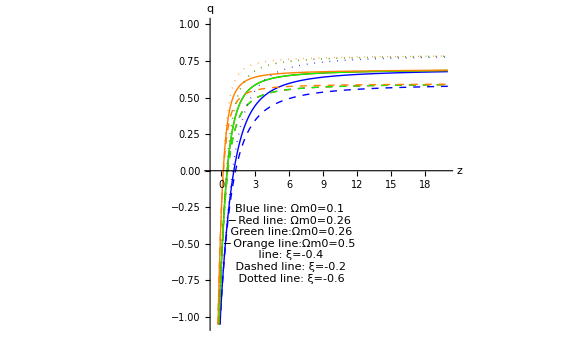

```mathematica
pldecICCPLShowSum
```

To check the effect of different parameters.

```mathematica
varyingICCPLShowSum
```

Varying CPL w0 | Varying CPL w1 | Varying Ωm0 | Varying ξ
-Graphics- | -Graphics- | -Graphics- | -Graphics-

A toy to play with the curve.

```mathematica
pldecICCPLManSum
```

A plot shows how bad it is to use transition redshift to constrain interacting model. This is a CPL parameterized example. For ξ∈(-0.8,0), the line just stays near the allowed region constrained by Riess’s results.

```mathematica
pldecrICCPLDense
```

-Graphics-